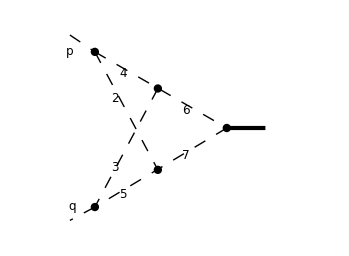
-Graphics-
(*The first entry in the basis, see below, is the irreducible numerator*)

```mathematica
(* diagram comes from the LiteRed package*)
```

```mathematica
(*generate a start file*)
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../"];
Get["FIRE6.m"];
Internal= {l,r};
External= {p,q};
Propagators=(- Power[##,2])&/@{l-r,l,r,p-l,q-r,p-l+r,q-r+l};
Replacements= {p^2->0,q^2->0,p q->-1/2};
PrepareIBP[];
Prepare[AutoDetectRestrictions->True,LI->True];
SaveStart["examples/v2"];
```

FIRE, version 6.2.dev

Prepared

Dimension set to 7

No symmetries

Saving initial data

```mathematica
Quit
```

```mathematica
(* reduction purely by FIRE *)
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../"];
Get["FIRE6.m"];
LoadStart["examples/v2",2];
Burn[]
```

FIRE, version 6.2.dev

Initial data loaded

True

```mathematica
F[2,{-1,1,1,1,1,1,1}]
```

EVALUATING {2,{-1,1,1,1,1,1,1}}

Working in sector 3/49: {2,{-1,1,1,1,1,1,1}}

LAPORTA STARTED: 1 integrals for evaluation

Maximal levels: {{0,1}}

{1,1}

Preparing points, symmetries and 117 IBP's: 0.1191 seconds.

MEMORY INFORMATION: 100 MEGABYTES REACHED

76 new relations produced: 0.751135 seconds.

IRREDUCIBLE INTEGRAL: {2,{0,1,1,1,1,1,1}}

Sector complete

Working in sector 9/49: {2,{-1,1,1,1,1,1,-1}}

LAPORTA STARTED: 4 integrals for evaluation

Maximal levels: {{1,1}}

{1,1}

Preparing points, symmetries and 147 IBP's: 0.11177 seconds.

16 new relations produced: 0.071417 seconds.

Sector complete

Working in sector 11/49: {2,{-1,-1,1,1,1,1,1}}

LAPORTA STARTED: 9 integrals for evaluation

Maximal levels: {{1,1}}

{1,1}

Preparing points, symmetries and 150 IBP's: 0.11231 seconds.

71 new relations produced: 0.638597 seconds.

Sector complete

Working in sector 13/49: {2,{-1,1,-1,1,1,1,1}}

LAPORTA STARTED: 4 integrals for evaluation

Maximal levels: {{1,1}}

{1,1}

Preparing points, symmetries and 153 IBP's: 0.13905 seconds.

63 new relations produced: 0.54917 seconds.

Sector complete

Working in sector 16/49: {2,{-1,1,1,-1,1,1,1}}

LAPORTA STARTED: 2 integrals for evaluation

Maximal levels: {{1,1}}

{1,1}

Preparing points, symmetries and 153 IBP's: 0.11525 seconds.

9 new relations produced: 0.065909 seconds.

Sector complete

Working in sector 19/49: {2,{-1,1,1,1,-1,1,1}}

LAPORTA STARTED: 3 integrals for evaluation

Maximal levels: {{1,1}}

{1,1}

Preparing points, symmetries and 150 IBP's: 0.17325 seconds.

9 new relations produced: 0.054363 seconds.

Sector complete

Working in sector 28/49: {2,{-1,1,-1,1,1,1,-1}}

LAPORTA STARTED: 15 integrals for evaluation

Maximal levels: {{2,1}}

{1,1}

Preparing points, symmetries and 164 IBP's: 0.097261 seconds.

119 new relations produced: 0.630064 seconds.

{1,2}

Preparing points, symmetries and 232 IBP's: 0.09462 seconds.

135 new relations produced: 0.762816 seconds.

{2,1}

Preparing points, symmetries and 296 IBP's: 0.13842 seconds.

69 new relations produced: 0.24373 seconds.

Sector complete

Working in sector 30/49: {2,{-1,-1,-1,1,1,1,1}}

LAPORTA STARTED: 14 integrals for evaluation

Maximal levels: {{2,0}}

{1,1}

Preparing points, symmetries and 168 IBP's: 0.07887 seconds.

125 new relations produced: 1.00842 seconds.

{2,1}

Preparing points, symmetries and 312 IBP's: 0.16254 seconds.

IRREDUCIBLE INTEGRAL: {2,{0,0,0,1,1,1,1}}

72 new relations produced: 0.518596 seconds.

Sector complete

Working in sector 31/49: {2,{-1,1,1,-1,1,1,-1}}

LAPORTA STARTED: 6 integrals for evaluation

Maximal levels: {{2,1}}

{1,1}

Preparing points, symmetries and 164 IBP's: 0.084907 seconds.

60 new relations produced: 0.19743 seconds.

Sector complete

Working in sector 33/49: {2,{-1,-1,1,-1,1,1,1}}

LAPORTA STARTED: 8 integrals for evaluation

Maximal levels: {{2,1}}

{1,1}

Preparing points, symmetries and 168 IBP's: 0.095222 seconds.

51 new relations produced: 0.21012 seconds.

Sector complete

Working in sector 35/49: {2,{-1,1,-1,-1,1,1,1}}

LAPORTA STARTED: 10 integrals for evaluation

Maximal levels: {{2,1}}

{1,1}

Preparing points, symmetries and 171 IBP's: 0.088041 seconds.

113 new relations produced: 0.687319 seconds.

{1,2}

Preparing points, symmetries and 243 IBP's: 0.12197 seconds.

133 new relations produced: 1.14701 seconds.

{2,1}

Preparing points, symmetries and 324 IBP's: 0.1426 seconds.

11 new relations produced: 0.039673 seconds.

Sector complete

Working in sector 36/49: {2,{-1,-1,1,1,-1,1,1}}

LAPORTA STARTED: 12 integrals for evaluation

Maximal levels: {{2,1}}

{1,1}

Preparing points, symmetries and 168 IBP's: 0.080781 seconds.

113 new relations produced: 0.709807 seconds.

{1,2}

Preparing points, symmetries and 238 IBP's: 0.098832 seconds.

133 new relations produced: 1.22323 seconds.

{2,1}

Preparing points, symmetries and 312 IBP's: 0.17181 seconds.

82 new relations produced: 0.575055 seconds.

Sector complete

Working in sector 37/49: {2,{-1,1,-1,1,-1,1,1}}

LAPORTA STARTED: 10 integrals for evaluation

Maximal levels: {{2,1}}

{1,1}

Preparing points, symmetries and 168 IBP's: 0.10888 seconds.

74 new relations produced: 0.31809 seconds.

Sector complete

Working in sector 38/49: {2,{-1,1,1,-1,-1,1,1}}

LAPORTA STARTED: 4 integrals for evaluation

Maximal levels: {{1,0}}

{1,1}

Preparing points, symmetries and 168 IBP's: 0.087556 seconds.

125 new relations produced: 0.798506 seconds.

IRREDUCIBLE INTEGRAL: {2,{0,1,1,0,0,1,1}}

Sector complete

Working in sector 41/49: {2,{-1,-1,1,1,1,-1,1}}

LAPORTA STARTED: 12 integrals for evaluation

Maximal levels: {{2,1}}

{1,1}

Preparing points, symmetries and 164 IBP's: 0.075366 seconds.

119 new relations produced: 0.485649 seconds.

{1,2}

Preparing points, symmetries and 232 IBP's: 0.093954 seconds.

135 new relations produced: 0.732732 seconds.

{2,1}

Preparing points, symmetries and 296 IBP's: 0.12709 seconds.

45 new relations produced: 0.14727 seconds.

Sector complete

Working in sector 44/49: {2,{-1,1,1,1,-1,-1,1}}

LAPORTA STARTED: 2 integrals for evaluation

Maximal levels: {{1,0}}

{1,1}

Preparing points, symmetries and 164 IBP's: 0.083671 seconds.

60 new relations produced: 0.1812 seconds.

Sector complete

Working in sector 47/49: {2,{-1,1,-1,-1,1,1,-1}}

LAPORTA STARTED: 16 integrals for evaluation

Maximal levels: {{3,0}}

{1,1}

Preparing points, symmetries and 164 IBP's: 0.057756 seconds.

127 new relations produced: 0.584874 seconds.

{2,1}

Preparing points, symmetries and 222 IBP's: 0.10548 seconds.

147 new relations produced: 0.869738 seconds.

{3,1}

Preparing points, symmetries and 354 IBP's: 0.14687 seconds.

IRREDUCIBLE INTEGRAL: {2,{0,1,0,0,1,1,0}}

69 new relations produced: 0.29776 seconds.

Sector complete

Working in sector 49/49: {2,{-1,-1,1,1,-1,-1,1}}

LAPORTA STARTED: 20 integrals for evaluation

Maximal levels: {{3,1}}

{1,1}

Preparing points, symmetries and 164 IBP's: 0.065723 seconds.

127 new relations produced: 0.645545 seconds.

{1,2}

Preparing points, symmetries and 306 IBP's: 0.11099 seconds.

187 new relations produced: 1.16417 seconds.

{2,1}

Preparing points, symmetries and 222 IBP's: 0.099893 seconds.

147 new relations produced: 0.817929 seconds.

{2,2}

Preparing points, symmetries and 378 IBP's: 0.14571 seconds.

200 new relations produced: 1.31493 seconds.

{3,1}

Preparing points, symmetries and 354 IBP's: 0.14415 seconds.

IRREDUCIBLE INTEGRAL: {2,{0,0,1,1,0,0,1}}

93 new relations produced: 0.388851 seconds.

Sector complete

SORTING THE LIST OF 1670 INTEGRALS: 0.072521 seconds.

Substituting 1670 values: 0.71617 seconds.

Total time: 24.08861 seconds

((-3+d) (-10+3 d) G[2,{0,0,0,1,1,1,1}])/(2 (-4+d)^2)+((-3+d) (-10+3 d) (-8+3 d) G[2,{0,0,1,1,0,0,1}])/(2 (-4+d)^3)+((-3+d) (-10+3 d) (-8+3 d) G[2,{0,1,0,0,1,1,0}])/(2 (-4+d)^3)-((-3+d) (-10+3 d) G[2,{0,1,1,0,0,1,1}])/(2 (-4+d)^2)-1/2 G[2,{0,1,1,1,1,1,1}]

```mathematica
(* master integrals ... too many *)
```

```mathematica
MasterIntegrals[]
```

{{2,{0,1,1,1,1,1,1}},{2,{0,0,0,1,1,1,1}},{2,{0,1,0,0,1,1,0}},{2,{0,0,1,1,0,0,1}},{2,{0,1,1,0,0,1,1}}}

```mathematica
(*finding relations between them*)
```

```mathematica
list=MasterIntegrals[];
Internal= {l,r};
External= {p,q};
Propagators= Power[##,2]&/@{l-r,l,r,p-l,q-r,p-l+r,q-r+l};
Replacements= {p^2->0,q^2->0,p q->-1/2};
WriteRules[list,"examples/v2"];
```

Input: 5, output: 3

Saving rules

```mathematica
(*we are left with 3*)
```

```mathematica
Union@@((G@@@list)/.FindRules[list])
```

Input: 5, output: 3

G[2,{0,0,1,1,0,0,1},{0,1,1,0,0,1,1},{0,1,1,1,1,1,1}]

```mathematica
Quit
```

```mathematica
(*reduction with rules for masters*)
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../"];
Get["FIRE6.m"];
LoadStart["examples/v2",2];
Burn[];
LoadRules["examples/v2",2];
```

FIRE, version 6.2.dev

Initial data loaded

```mathematica
F[2,{-1,1,1,1,1,1,1}]
```

EVALUATING {2,{-1,1,1,1,1,1,1}}

Working in sector 3/49: {2,{-1,1,1,1,1,1,1}}

LAPORTA STARTED: 1 integrals for evaluation

Maximal levels: {{0,1}}

{1,1}

Preparing points, symmetries and 117 IBP's: 0.066317 seconds.

MEMORY INFORMATION: 100 MEGABYTES REACHED

76 new relations produced: 0.459955 seconds.

IRREDUCIBLE INTEGRAL: {2,{0,1,1,1,1,1,1}}

Sector complete

Working in sector 9/49: {2,{-1,1,1,1,1,1,-1}}

LAPORTA STARTED: 4 integrals for evaluation

Maximal levels: {{1,1}}

{1,1}

Preparing points, symmetries and 147 IBP's: 0.088182 seconds.

16 new relations produced: 0.051438 seconds.

Sector complete

Working in sector 11/49: {2,{-1,-1,1,1,1,1,1}}

LAPORTA STARTED: 9 integrals for evaluation

Maximal levels: {{1,1}}

{1,1}

Preparing points, symmetries and 150 IBP's: 0.070634 seconds.

71 new relations produced: 0.35269 seconds.

Sector complete

Working in sector 13/49: {2,{-1,1,-1,1,1,1,1}}

LAPORTA STARTED: 4 integrals for evaluation

Maximal levels: {{1,1}}

{1,1}

Preparing points, symmetries and 153 IBP's: 0.06525 seconds.

63 new relations produced: 0.30532 seconds.

Sector complete

Working in sector 16/49: {2,{-1,1,1,-1,1,1,1}}

LAPORTA STARTED: 2 integrals for evaluation

Maximal levels: {{1,1}}

{1,1}

Preparing points, symmetries and 153 IBP's: 0.068117 seconds.

9 new relations produced: 0.036647 seconds.

Sector complete

Working in sector 19/49: {2,{-1,1,1,1,-1,1,1}}

LAPORTA STARTED: 3 integrals for evaluation

Maximal levels: {{1,1}}

{1,1}

Preparing points, symmetries and 150 IBP's: 0.068932 seconds.

9 new relations produced: 0.047637 seconds.

Sector complete

Working in sector 28/49: {2,{-1,1,-1,1,1,1,-1}}

LAPORTA STARTED: 15 integrals for evaluation

Maximal levels: {{2,1}}

{1,1}

Preparing points, symmetries and 164 IBP's: 0.073567 seconds.

119 new relations produced: 0.493805 seconds.

{1,2}

Preparing points, symmetries and 232 IBP's: 0.092171 seconds.

135 new relations produced: 0.752149 seconds.

{2,1}

Preparing points, symmetries and 296 IBP's: 0.12782 seconds.

69 new relations produced: 0.24057 seconds.

Sector complete

Working in sector 30/49: {2,{-1,-1,-1,1,1,1,1}}

LAPORTA STARTED: 14 integrals for evaluation

Maximal levels: {{2,0}}

{1,1}

Preparing points, symmetries and 168 IBP's: 0.078496 seconds.

125 new relations produced: 0.766096 seconds.

{2,1}

Preparing points, symmetries and 312 IBP's: 0.13291 seconds.

72 new relations produced: 0.361585 seconds.

Sector complete

Working in sector 31/49: {2,{-1,1,1,-1,1,1,-1}}

LAPORTA STARTED: 6 integrals for evaluation

Maximal levels: {{2,1}}

{1,1}

Preparing points, symmetries and 164 IBP's: 0.078479 seconds.

60 new relations produced: 0.19057 seconds.

Sector complete

Working in sector 33/49: {2,{-1,-1,1,-1,1,1,1}}

LAPORTA STARTED: 8 integrals for evaluation

Maximal levels: {{2,1}}

{1,1}

Preparing points, symmetries and 168 IBP's: 0.077724 seconds.

51 new relations produced: 0.20776 seconds.

Sector complete

Working in sector 35/49: {2,{-1,1,-1,-1,1,1,1}}

LAPORTA STARTED: 10 integrals for evaluation

Maximal levels: {{2,1}}

{1,1}

Preparing points, symmetries and 171 IBP's: 0.083398 seconds.

113 new relations produced: 0.586476 seconds.

{1,2}

Preparing points, symmetries and 243 IBP's: 0.093554 seconds.

133 new relations produced: 0.940754 seconds.

{2,1}

Preparing points, symmetries and 324 IBP's: 0.12927 seconds.

11 new relations produced: 0.039467 seconds.

Sector complete

Working in sector 36/49: {2,{-1,-1,1,1,-1,1,1}}

LAPORTA STARTED: 12 integrals for evaluation

Maximal levels: {{2,1}}

{1,1}

Preparing points, symmetries and 168 IBP's: 0.081886 seconds.

113 new relations produced: 0.635088 seconds.

{1,2}

Preparing points, symmetries and 238 IBP's: 0.086862 seconds.

133 new relations produced: 1.01404 seconds.

{2,1}

Preparing points, symmetries and 312 IBP's: 0.13088 seconds.

82 new relations produced: 0.387936 seconds.

Sector complete

Working in sector 37/49: {2,{-1,1,-1,1,-1,1,1}}

LAPORTA STARTED: 10 integrals for evaluation

Maximal levels: {{2,1}}

{1,1}

Preparing points, symmetries and 168 IBP's: 0.077738 seconds.

74 new relations produced: 0.31213 seconds.

Sector complete

Working in sector 38/49: {2,{-1,1,1,-1,-1,1,1}}

LAPORTA STARTED: 5 integrals for evaluation

Maximal levels: {{1,0}}

{1,1}

Preparing points, symmetries and 168 IBP's: 0.093077 seconds.

125 new relations produced: 0.729648 seconds.

IRREDUCIBLE INTEGRAL: {2,{0,1,1,0,0,1,1}}

Sector complete

Working in sector 41/49: {2,{-1,-1,1,1,1,-1,1}}

LAPORTA STARTED: 12 integrals for evaluation

Maximal levels: {{2,1}}

{1,1}

Preparing points, symmetries and 164 IBP's: 0.081287 seconds.

119 new relations produced: 0.475408 seconds.

{1,2}

Preparing points, symmetries and 232 IBP's: 0.087142 seconds.

135 new relations produced: 0.728067 seconds.

{2,1}

Preparing points, symmetries and 296 IBP's: 0.12712 seconds.

45 new relations produced: 0.14136 seconds.

Sector complete

Working in sector 44/49: {2,{-1,1,1,1,-1,-1,1}}

LAPORTA STARTED: 2 integrals for evaluation

Maximal levels: {{1,0}}

{1,1}

Preparing points, symmetries and 164 IBP's: 0.089154 seconds.

60 new relations produced: 0.17808 seconds.

Sector complete

Working in sector 47/49: {2,{-1,1,-1,-1,1,1,-1}}

LAPORTA STARTED: 16 integrals for evaluation

Maximal levels: {{3,0}}

{1,1}

Preparing points, symmetries and 164 IBP's: 0.061017 seconds.

127 new relations produced: 0.515464 seconds.

{2,1}

Preparing points, symmetries and 222 IBP's: 0.095001 seconds.

147 new relations produced: 0.590317 seconds.

{3,1}

Preparing points, symmetries and 354 IBP's: 0.14655 seconds.

69 new relations produced: 0.21815 seconds.

Sector complete

Working in sector 49/49: {2,{-1,-1,1,1,-1,-1,1}}

LAPORTA STARTED: 21 integrals for evaluation

Maximal levels: {{3,1}}

{1,1}

Preparing points, symmetries and 164 IBP's: 0.064603 seconds.

127 new relations produced: 0.570583 seconds.

{1,2}

Preparing points, symmetries and 306 IBP's: 0.11054 seconds.

187 new relations produced: 1.13336 seconds.

{2,1}

Preparing points, symmetries and 222 IBP's: 0.096847 seconds.

147 new relations produced: 0.782388 seconds.

{2,2}

Preparing points, symmetries and 378 IBP's: 0.14816 seconds.

200 new relations produced: 1.3115 seconds.

{3,1}

Preparing points, symmetries and 354 IBP's: 0.14759 seconds.

IRREDUCIBLE INTEGRAL: {2,{0,0,1,1,0,0,1}}

93 new relations produced: 0.387054 seconds.

Sector complete

SORTING THE LIST OF 1679 INTEGRALS: 0.076342 seconds.

Substituting 1679 values: 0.855833 seconds.

Total time: 20.62986 seconds

((-3+d) (-10+3 d) (-8+3 d) G[2,{0,0,1,1,0,0,1}])/(-4+d)^3-1/2 G[2,{0,1,1,1,1,1,1}]

```mathematica
Quit
```

```mathematica
(*generate LiteRed bases*)
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../"];
SetDirectory["extra/LiteRed/Setup/"];
Get["LiteRed.m"];
SetDirectory["../../../"];
Get["FIRE6.m"];
Internal= {l,r};
External= {p,q};
Propagators= (-Power[##,2])&/@{l-r,l,r,p-l,q-r,p-l+r,q-r+l};
Replacements= {p^2->0,q^2->0,p q->-1/2};
CreateNewBasis[v2,Directory->"temp/v2.dir"]
```

**************** LiteRed v1.82 ********************
Author: Roman N. Lee, Budker Institute of Nuclear Physics, Novosibirsk.
Release Date: 01.06.2015
LiteRed stands for Loop InTEgrals REDuction.
The package is designed for the search and application of the Integration-By-Part reduction rules. It also contains some other useful tools.
See ?LiteRed`* for a list of functions.

FIRE, version 6.2.dev

Declare: {{l,r,p,q},Vector}

Lee propagators: {-((l-r)·(l-r)),-(l·l),-(r·r),-((-l+p)·(-l+p)),-((q-r)·(q-r)),-((-l+p+r)·(-l+p+r)),-((l+q-r)·(l+q-r))}

Valid basis.
    Ds[v2] — denominators,
    SPs[v2] — scalar products involving loop momenta,
    LMs[v2] — loop momenta,
    EMs[v2] — external momenta,
    Toj[v2] — rules to transform scalar products to denominators.
The definitions of the basis will be saved in temp/v2.dir

DiskSave::dir: The directory temp/v2.dir has been created.

```mathematica
GenerateIBP[v2];
AnalyzeSectors[v2,{0,__}];
FindSymmetries[v2];
SetOptions[SolvejSector,Depth->0];
SolvejSector/@UniqueSectors[v2];
DiskSave[v2];
```

Integration-By-Part&Lorentz-Invariance identities are generated.
    IBP[v2] — integration-by-part identities,
    LI[v2] — Lorentz invariance identities.

Found 47 zero sectors out of 64.
    ZeroSectors[v2] — zero sectors,
    NonZeroSectors[v2] — nonzero sectors,
    SimpleSectors[v2] — simple sectors (no nonzero subsectors),
    BasisSectors[v2] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[v2] — a rule to nullify all zero j[v2…],
    CutDs[v2] — a flag list of cut denominatorsj (1=cut).

Found 8 mapped sectors and 9 unique sectors.
    UniqueSectors[v2] — unique sectors.
    MappedSectors[v2] — mapped sectors.
    SR[v2][…] — symmetry relations for j[v2,…] from UniqueSectors[v2].
    jSymmetries[v2,…] — symmetry rules for the sector js[v2,…] in UniqueSectors[v2].
    jRules[v2,…] — reduction rules for j[v2,…] from MappedSectors[v2].

Sector js[v2,0,0,1,1,0,0,1]

1 master integrals found:
j[v2, 0, 0, 1, 1, 0, 0, 1].
    jRules[v2, 0, 0, 1, 1, 0, 0, 1] — reduction rules for the sector.
    MIs[v2] — updated list of the masters.

Sector js[v2,0,0,0,1,1,1,1]

1 master integrals found:
j[v2, 0, 0, 0, 1, 1, 1, 1].
    jRules[v2, 0, 0, 0, 1, 1, 1, 1] — reduction rules for the sector.
    MIs[v2] — updated list of the masters.

Sector js[v2,0,0,1,1,0,1,1]

0 master integrals found.
    jRules[v2, 0, 0, 1, 1, 0, 1, 1] — reduction rules for the sector.
    MIs[v2] — updated list of the masters.

Sector js[v2,0,0,1,1,1,0,1]

0 master integrals found.
    jRules[v2, 0, 0, 1, 1, 1, 0, 1] — reduction rules for the sector.
    MIs[v2] — updated list of the masters.

Sector js[v2,0,1,0,1,1,1,0]

0 master integrals found.
    jRules[v2, 0, 1, 0, 1, 1, 1, 0] — reduction rules for the sector.
    MIs[v2] — updated list of the masters.

Sector js[v2,0,0,1,1,1,1,1]

0 master integrals found.
    jRules[v2, 0, 0, 1, 1, 1, 1, 1] — reduction rules for the sector.
    MIs[v2] — updated list of the masters.

Sector js[v2,0,1,0,1,1,1,1]

0 master integrals found.
    jRules[v2, 0, 1, 0, 1, 1, 1, 1] — reduction rules for the sector.
    MIs[v2] — updated list of the masters.

Sector js[v2,0,1,1,1,1,0,1]

0 master integrals found.
    jRules[v2, 0, 1, 1, 1, 1, 0, 1] — reduction rules for the sector.
    MIs[v2] — updated list of the masters.

Sector js[v2,0,1,1,1,1,1,1]

1 master integrals found:
j[v2, 0, 1, 1, 1, 1, 1, 1].
    jRules[v2, 0, 1, 1, 1, 1, 1, 1] — reduction rules for the sector.
    MIs[v2] — updated list of the masters.

DiskSave::overwrite: The file temp/v2.dir/v2 has been overwritten.

```mathematica
Quit
```

```mathematica
(*reduction with LiteRed rules*)
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../"];
Get["FIRE6.m"];
LoadStart["examples/v2",2];
LoadLRules["temp/v2.dir",2];
Burn[]
```

FIRE, version 6.2.dev

Initial data loaded

True

```mathematica
F[2,{-1,1,1,1,1,1,1}]
```

EVALUATING {2,{-1,1,1,1,1,1,1}}

Working in sector 3/46: {2,{-1,1,1,1,1,1,1}}

MEMORY INFORMATION: 100 MEGABYTES REACHED

IRREDUCIBLE INTEGRAL: {2,{0,1,1,1,1,1,1}}

2 new relations produced: 0.0132 seconds

Working in sector 9/46: {2,{-1,1,1,1,1,1,-1}}

2 new relations produced: 0.009 seconds

Working in sector 11/46: {2,{-1,1,1,1,-1,1,1}}

1 new relations produced: 0.007105 seconds

Working in sector 13/46: {2,{-1,-1,1,1,1,1,1}}

4 new relations produced: 0.02352 seconds

Working in sector 15/46: {2,{-1,1,-1,1,1,1,1}}

5 new relations produced: 0.02191 seconds

Working in sector 24/46: {2,{-1,1,1,1,1,-1,1}}

5 new relations produced: 0.009999 seconds

Working in sector 29/46: {2,{-1,1,-1,-1,1,1,1}}

2 new relations produced: 0.00201 seconds

Working in sector 31/46: {2,{-1,1,1,1,-1,-1,1}}

3 new relations produced: 0.004349 seconds

Working in sector 32/46: {2,{-1,1,-1,1,1,1,-1}}

6 new relations produced: 0.009214 seconds

Working in sector 34/46: {2,{-1,-1,-1,1,1,1,1}}

IRREDUCIBLE INTEGRAL: {2,{0,0,0,1,1,1,1}}

3 new relations produced: 0.01145 seconds

Working in sector 37/46: {2,{-1,-1,1,1,-1,1,1}}

4 new relations produced: 0.007977 seconds

Working in sector 39/46: {2,{-1,-1,1,1,1,-1,1}}

3 new relations produced: 0.004228 seconds

Working in sector 44/46: {2,{-1,1,-1,-1,1,1,-1}}

4 new relations produced: 0.00489 seconds

Working in sector 46/46: {2,{-1,-1,1,1,-1,-1,1}}

IRREDUCIBLE INTEGRAL: {2,{0,0,1,1,0,0,1}}

12 new relations produced: 0.02239 seconds

GENERATING 53 NEW RELATIONS: 0.16084 seconds.

SORTING THE LIST OF 56 INTEGRALS: 0.00157 seconds.

Substituting 56 values: 0.075349 seconds.

Total time: 0.24357 seconds

((-3+d) (-10+3 d) (-8+3 d) G[2,{0,0,1,1,0,0,1}])/(-4+d)^3-1/2 G[2,{0,1,1,1,1,1,1}]

```mathematica
Quit
```

```mathematica
(*we transform the LiteRed rules into a file for c++ FIRE*)
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../"];
Get["FIRE6.m"];
LoadStart["examples/v2"]; (*pay attention! there is no number as second argument here*)
```

FIRE, version 6.2.dev

Initial data loaded

```mathematica
TransformRules["temp/v2.dir","examples/v2.lbases",2];
```

1: jRules[v2, 0, 0, 0, 1, 1, 1, 1]

2: jRules[v2, 0, 0, 1, 1, 0, 0, 1]

3: jRules[v2, 0, 0, 1, 1, 0, 1, 1]

4: jRules[v2, 0, 0, 1, 1, 1, 0, 1]

5: jRules[v2, 0, 0, 1, 1, 1, 1, 1]

6: jRules[v2, 0, 1, 0, 0, 1, 1, 0]

7: jRules[v2, 0, 1, 0, 0, 1, 1, 1]

8: jRules[v2, 0, 1, 0, 1, 1, 1, 0]

9: jRules[v2, 0, 1, 0, 1, 1, 1, 1]

10: jRules[v2, 0, 1, 1, 0, 0, 1, 1]

11: jRules[v2, 0, 1, 1, 0, 1, 1, 0]

12: jRules[v2, 0, 1, 1, 0, 1, 1, 1]

13: jRules[v2, 0, 1, 1, 1, 0, 0, 1]

14: jRules[v2, 0, 1, 1, 1, 0, 1, 1]

15: jRules[v2, 0, 1, 1, 1, 1, 0, 1]

16: jRules[v2, 0, 1, 1, 1, 1, 1, 0]

17: jRules[v2, 0, 1, 1, 1, 1, 1, 1]

1: jSymmetries[v2, 0, 0, 0, 1, 1, 1, 1]

2: jSymmetries[v2, 0, 0, 1, 1, 0, 0, 1]

3: jSymmetries[v2, 0, 0, 1, 1, 0, 1, 1]

4: jSymmetries[v2, 0, 0, 1, 1, 1, 0, 1]

5: jSymmetries[v2, 0, 0, 1, 1, 1, 1, 1]

6: jSymmetries[v2, 0, 1, 0, 1, 1, 1, 0]

7: jSymmetries[v2, 0, 1, 0, 1, 1, 1, 1]

8: jSymmetries[v2, 0, 1, 1, 1, 1, 0, 1]

9: jSymmetries[v2, 0, 1, 1, 1, 1, 1, 1]

```mathematica
SaveSBases["examples/v2"];
```

Saving the bases

```mathematica
(*now run examples/v2l for the reduction with the use of the converted file*)
```